```mathematica
LaunchKernels[]
```

{KernelObject[9,local],KernelObject[10,local],KernelObject[11,local],KernelObject[12,local]}

```mathematica
CloseKernels[]
```

{KernelObject[9,local,<defunct>],KernelObject[10,local,<defunct>],KernelObject[11,local,<defunct>],KernelObject[12,local,<defunct>]}

```mathematica
LaunchKernels[]
```

{KernelObject[13,local],KernelObject[14,local],KernelObject[15,local],KernelObject[16,local]}

# Thermal Conductivity by numeric integration

```mathematica
SetDirectory[]
SetDirectory["Documents/Wolfram Mathematica/Dzyaloshinskii_Moriya/"]
Directory[]
```

/home/benjamin

/home/benjamin/Documents/Wolfram Mathematica/Dzyaloshinskii_Moriya

/home/benjamin/Documents/Wolfram Mathematica/Dzyaloshinskii_Moriya

NIntegrate::inumri: The integrand -(6.65613×10^7 (Cos[kx]+Cos[ky])^2 (Sin[kx]^2+Sin[ky]^2))/(1-Cosh[32634. √Times[«2»]]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,9.35762×10^-14},{0,1}}.

NIntegrate::inumri: The integrand -(6.65613×10^7 (0.+1. (Cos[kx]+Cos[ky]))^2 (Sin[kx]^2+Sin[ky]^2))/(1-Cosh[32634. √Times[«2»]]) has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{0.,9.35762×10^-14},{0,1}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

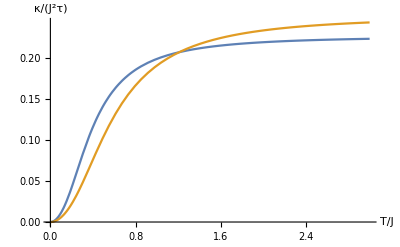

```mathematica
J=1;
S=1/2;
γ[kx_,ky_]:=1/2*(Cos[kx]+Cos[ky]);
ϵ[kx_,ky_,d_]:=4*S*Sqrt[(1-γ[kx,ky])*(d^2+J^2+J*Sqrt[d^2+J^2]*γ[kx,ky])];
heatconductivitydensity[kx_,ky_,d_,β_,ξ_]:=-(4 S^2 (d^2+J (J-√(d^2+J^2))+J √(d^2+J^2) (Cos[kx]+Cos[ky])))^2*(Sin[kx]^2+Sin[ky]^2)*(β^2/2)/(1-Cosh[β*ϵ[kx,ky,d]])*(1)/(2*ξ);
Plot[{1/(4π^2)*NIntegrate[heatconductivitydensity[kx,ky,0,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],1/(4π^2)*NIntegrate[heatconductivitydensity[kx,ky,1,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0,3},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

```mathematica
Manipulate[Plot[{ϵ[x,x,d],Sqrt[32*S^2*(d^2+J^2-J*Sqrt[d^2+J^2])]},{x,-π,π},PlotRange->All],{d,0,3}]
```

```mathematica
Manipulate[Plot[{2*S*Sqrt[2]x*Sqrt[d^2+J^2+J*Sqrt[d^2+J^2]],ϵ[x,x,d]},{x,0,.5},PlotRange->All],{d,0,1}]
```

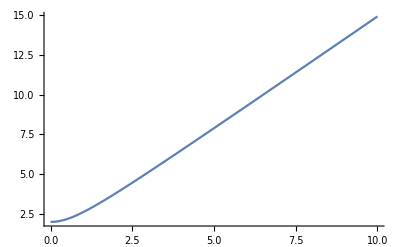

```mathematica
Plot[2*S*Sqrt[2]*Sqrt[d^2+J^2+J*Sqrt[d^2+J^2]],{d,0,10}]
```

## Plot for different fields

```mathematica
plotlist=ParallelTable[Table[{T,NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->64]},{T,0.01,3,0.001}],{d,0,1,0.1}];
```

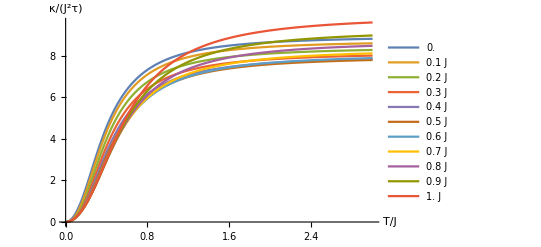

```mathematica
ListPlot[plotlist,Joined->True,PlotLegends->Table["J" N[i],{i,0,1,1/(Length[plotlist]-1)}],AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

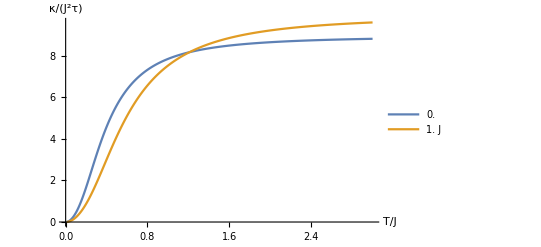

```mathematica
ListPlot[{plotlist[[1]],plotlist[[11]]},Joined->True,PlotLegends->Table["J" N[i],{i,0,1}],AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

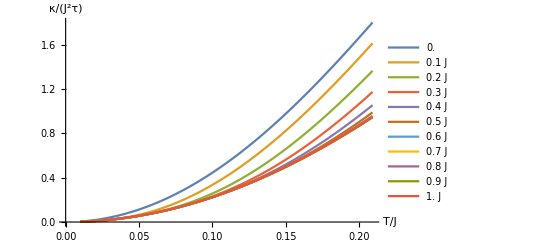

```mathematica
ListPlot[Table[Table[plotlist[[i]][[j]],{j,1,200}],{i,1,Length[plotlist]}],Joined->True,PlotLegends->Table["J" N[i],{i,0,1,1/(Length[plotlist]-1)}],AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

```mathematica
plotlist2=ParallelTable[Table[{T,NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->64]},{T,0.01,0.3,0.0001}],{d,0.99,1,0.001}];
```

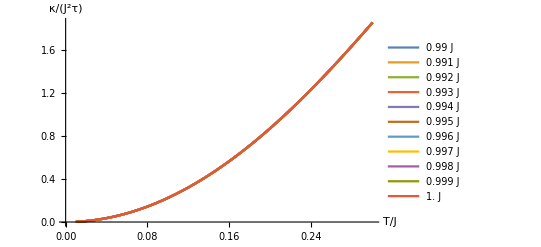

```mathematica
ListPlot[plotlist2[[1;;Length[plotlist2]]],PlotLegends->Table["J" N[i*0.01+0.99],{i,0,1,1/(Length[plotlist2]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

```mathematica
plotlist3=ParallelTable[Table[{T,NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->64]},{T,1/100,3/10,1/1000}],{d,0,1/10,1/100}];
```

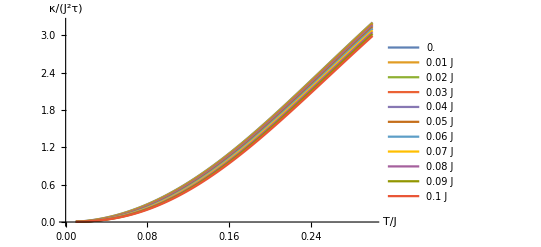

```mathematica
ListPlot[plotlist3[[1;;Length[plotlist3]]],PlotLegends->Table["J" N[i*0.1],{i,0,1,1/(Length[plotlist3]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

## Thermal Conductivity for narrowed Brillouin zone

center

```mathematica
Δ=π/10;
narrowedtocentersmallfield=ParallelTable[Table[{T,NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,1,0.01}],{d,0,0.1,0.01}];
narrowedtocenterlargefield=ParallelTable[Table[{T,NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.001,1,0.01}],{d,0.9,1,0.01}];
```

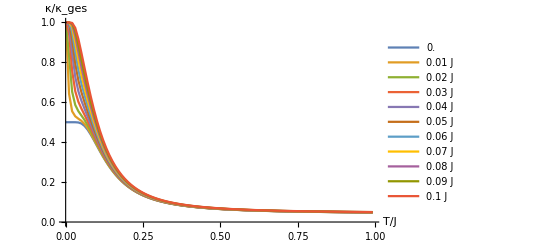

```mathematica
ListPlot[narrowedtocentersmallfield,PlotLegends->Table["J" N[0.1*i],{i,0,1,1/(Length[narrowedtocentersmallfield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

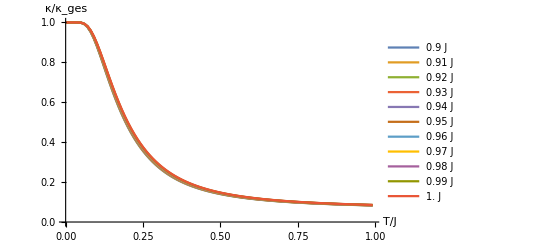

```mathematica
ListPlot[narrowedtocenterlargefield,PlotLegends->Table["J" N[i+0.9],{i,0,1,0.1/(Length[narrowedtocenterlargefield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

edges

```mathematica
narrowedtoedgessmallfield=ParallelTable[Table[{T,4*NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-π,-π+Δ},{ky,-π,-π+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.01,1.0,0.01}],{d,0,0.1,0.01}];
narrowedtoedgeslargefield=ParallelTable[Table[{T,4*NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-π,-π+Δ},{ky,-π,-π+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensity[kx,ky,d,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.01,1.0,0.01}],{d,0.9,1,0.01}];
```

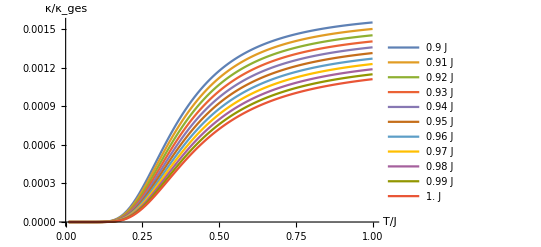

```mathematica
ListPlot[narrowedtoedgeslargefield,PlotLegends->Table["J" N[i+0.9],{i,0,1,0.1/(Length[narrowedtoedgeslargefield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

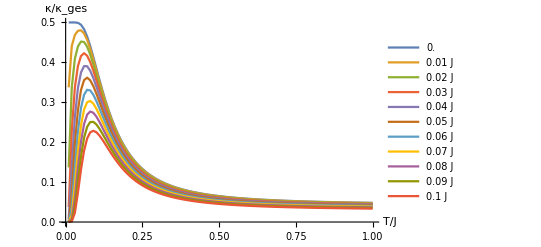

```mathematica
ListPlot[narrowedtoedgessmallfield,PlotLegends->Table["J" N[i],{i,0,1,0.1/(Length[narrowedtoedgessmallfield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

center and edges

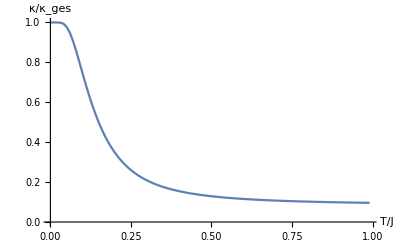

```mathematica
ListPlot[Table[{narrowedtocentersmallfield[[1]][[i]][[1]],narrowedtocentersmallfield[[1]][[i]][[2]]+narrowedtoedgessmallfield[[1]][[i]][[2]]},{i,1,Length[narrowedtocentersmallfield[[1]]]}],PlotRange->All,Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]}]
```

## Thermal conductivity for constant temperature but different fields

```mathematica
J=1;
S=1/2;
γ[kx_,ky_]:=1/2*(Cos[kx]+Cos[ky]);
ϵ[kx_,ky_,d_]:=4*S*Sqrt[(1-γ[kx,ky])*(d^2+J^2+J*Sqrt[d^2+J^2]*γ[kx,ky])];
heatconductivitydensity[kx_,ky_,d_,β_,ξ_]:=-(4 S^2 (d^2+J (J-√(d^2+J^2))+J √(d^2+J^2) (Cos[kx]+Cos[ky])))^2*(Sin[kx]^2)*(β^2/2)/(1-Cosh[β*ϵ[kx,ky,d]])*(1)/(2*ξ);
```

```mathematica
dlist=Table[{d,1/(4*π^2)*NIntegrate[heatconductivitydensity[kx,ky,d,1/0.3,0.01],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->64]},{d,0,1,1/100}];
```

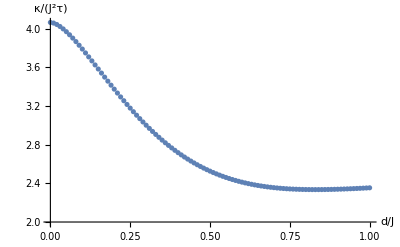

```mathematica
ListPlot[dlist,PlotRange->All,AxesLabel->{Style["d/J",18],Style["κ/(J^2τ)",18]},AxesOrigin->{0,2}]
```

```mathematica
test=Import["/home/benjamin/Documents/Programme/Square lattice/Heterostructure/Drudeweightoffield/drudeanalyticxsize1000ysize1000fieldsize1000.dat","Data"];
```

```mathematica
test[[1]]
```

{0,0.365632,-3.24096×10^-18,-3.23386×10^-18,0.365632}

```mathematica
numtest=Table[{test[[i]][[1]],test[[i]][[2]]/0.3^2},{i,1,Length[test]}];
```

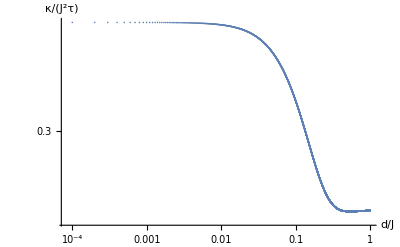

```mathematica
ListLogLogPlot[dlist,PlotRange->All,AxesLabel->{Style["d/J",18],Style["κ/(J^2τ)",18]}]
```

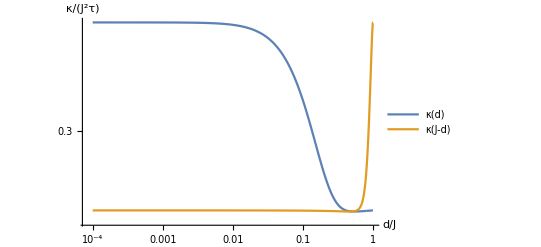

```mathematica
ListLogLogPlot[{dlist,Table[{1-dlist[[i]][[1]],dlist[[i]][[2]]},{i,1,Length[dlist]}]},PlotRange->All,AxesLabel->{Style["d/J",18],Style["κ/(J^2τ)",18]},PlotLegends->{"κ(d)","κ(J-d)"},Joined->True]
```

## asymptotic behaviour

entire Brillouin zone

```mathematica
list=Table[{Log[T],Log[NIntegrate[heatconductivitydensity[kx,ky,1,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]]},{T,1/100,2/10,1/10000}];
```

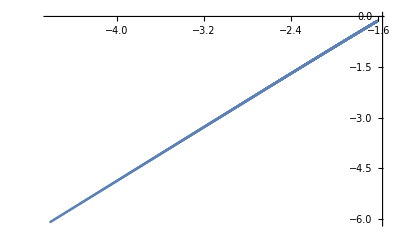

```mathematica
ListPlot[list,PlotRange->All]
```

```mathematica
Fit[list,{1,x},x]
```

3.07663+1.98719 x

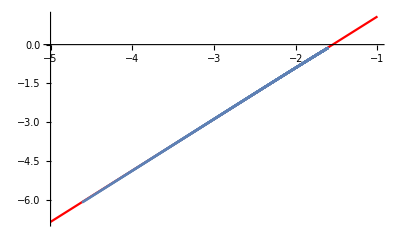

```mathematica
Show[Plot[3.076626597376663+1.987186406525642 x,{x,-5,-1},PlotStyle->Red],ListPlot[list]]
```

## sophisticated lifetimes

```mathematica
J=1;
z=4;
γ[kx_,ky_]:=1/2*(Cos[kx]+Cos[ky]);
ϵ[kx_,ky_,d_]:=4*S*Sqrt[(1-γ[kx,ky])*(d^2+J^2+J*Sqrt[d^2+J^2]*γ[kx,ky])];
heatconductivitydensityempiric[kx_,ky_,d_,β_,ξ_]=-(4 S^2 (d^2+J (J-√(d^2+J^2))+J √(d^2+J^2) (Cos[kx]+Cos[ky])))^2*(Sin[kx]^2+Sin[ky]^2)*(β^2/2)/(1-Cosh[β*ϵ[kx,ky,d]])*(1)/(2*ξ[##])&;
ξac[kx_,ky_,β_,d_]:=Sqrt[kx^2+ky^2]/(β^2*Sqrt[J^2+d^2+J*Sqrt[J^2+d^2]]);
ξmm[kx_,ky_,β_,d_]:=Sqrt[kx^2+ky^2]*Exp[-2.2*J*β];
ξgb[kx_,ky_,β_,d_]:=Sqrt[J^2+d^2+J*Sqrt[J^2+d^2]]/150;
ξcor[kx_,ky_,β_,d_]:=16*Sqrt[2]/(1.13*J*Exp[1.13*J*β]/(2.26*J+1/β));
ξcomb[kx_,ky_,β_,d_]:=Sqrt[J^2+0^2+J*Sqrt[J^2+0^2]]/150+Sqrt[kx^2+ky^2]/(β^2*Sqrt[J^2+d^2+J*Sqrt[J^2+0^2]]);
```

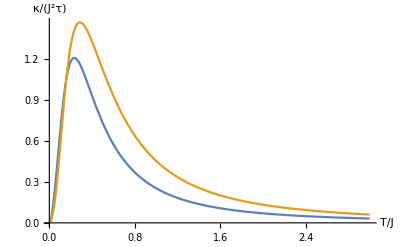

```mathematica
Plot[{1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,0,1/T,ξcomb][kx,ky,1/T,0],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,1,1/T,ξcomb][kx,ky,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.01,3},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["T/J",18],Style["κ/(J^2τ)",18]}]
```

```mathematica
Manipulate[DensityPlot[heatconductivitydensity[x,y,d,1/T,1],{x,-π,π},{y,-π,π},PlotRange->All],{d,0,1},{T,0.1,1}]
```

```mathematica
Manipulate[DensityPlot[heatconductivitydensityempiric[x,y,d,1/T,ξcomb][x,y,1/T,d],{x,-π,π},{y,-π,π},PlotRange->All,PlotLegends->Automatic],{d,0,1},{T,0.1,1}]
```

```mathematica
Manipulate[Plot[{heatconductivitydensityempiric[x,x,d,1/T,ξcomb][x,x,1/T,d]},{x,0,π},PlotRange->All],{T,0.01,10},{d,0.0,1}]
```

```mathematica
Manipulate[Plot[{heatconductivitydensity[x,x,d,1/T,1]},{x,0,π},PlotRange->All],{T,0.01,10},{d,0.0,1}]
```

```mathematica
Plot3D[1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100],{T,0.01,10},{d,0,1},AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["T/J",18],Style["D/J",18],Style["κ/(J^2τ)",18]},MeshFunctions->{#1&,#2&}]
```

-Graphics3D-

```mathematica
sophblist=ParallelTable[Table[{T,d,1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.1,0.3,0.00005}],{d,Flatten[{Table[0.01*i,{i,0,100}]}]}];
```

```mathematica
ListPointPlot3D[sophblist[[1;;(Length[sophblist])]],PlotRange->All,AxesLabel->{Style["T/J",18],Style["D/J",18],Style["κ/(J^2τ)",18]},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
Export["fulldata.out",Table[Flatten[{sophblist⟦1⟧⟦i⟧⟦1⟧,Flatten[Table[{sophblist⟦j⟧⟦i⟧⟦2⟧,sophblist⟦j⟧⟦i⟧⟦3⟧},{j,1,Length[sophblist]}]]}],{i,1,Length[sophblist⟦1⟧]}],"Table"];
```

```mathematica
smallblist=ParallelTable[Table[{T,d,1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.1,3,0.001}],{d,Flatten[{Table[0.01*i,{i,0,10}]}]}];
largeblist=ParallelTable[Table[{T,d,1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.1,3,0.001}],{d,Flatten[{Table[0.90+0.01*i,{i,1,10}]}]}];
```

```mathematica
ListPointPlot3D[smallblist,PlotRange->All,AxesLabel->{Style["T/J",18],Style["D/J",18],Style["κ/(J^2τ)",18]},Boxed->False,AxesOrigin->{0,0,0}]
```

-Graphics3D-

```mathematica
smallblistsmallT=ParallelTable[Table[{T,d,1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.005,0.5,0.001}],{d,Flatten[{Table[0.01*i,{i,0,20}]}]}];
```

```mathematica
ListPointPlot3D[smallblistsmallT[[1]][[1;;50]]]
```

-Graphics3D-

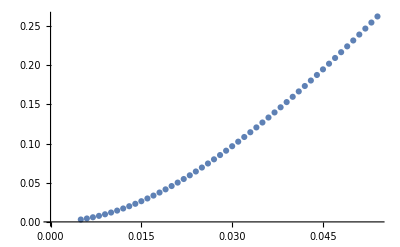

```mathematica
ListPlot[Table[{smallblistsmallT[[1]][[i]][[1]],smallblistsmallT[[1]][[i]][[3]]},{i,1,50}],AxesOrigin->{ 0,0}]
```

```mathematica
Export["smallbdata.out",Table[Flatten[{smallblist⟦1⟧⟦i⟧⟦1⟧,Flatten[Table[{smallblist⟦j⟧⟦i⟧⟦2⟧,smallblist⟦j⟧⟦i⟧⟦3⟧},{j,1,Length[smallblist]}]]}],{i,1,Length[smallblist⟦1⟧]}],"Table"];
```

```mathematica
ListPointPlot3D[largeblist,PlotRange->All,AxesLabel->{Style["T/J",18],Style["D/J",18],Style["κ/(J^2τ)",18]},Boxed->False,AxesOrigin->{0,1,0}]
```

-Graphics3D-

```mathematica
Export["largebdata.out",Table[Flatten[{largeblist⟦1⟧⟦i⟧⟦1⟧,Flatten[Table[{largeblist⟦j⟧⟦i⟧⟦2⟧,largeblist⟦j⟧⟦i⟧⟦3⟧},{j,1,Length[largeblist]}]]}],{i,1,Length[largeblist⟦1⟧]}],"Table"];
```

```mathematica
sophblistconstT=ParallelTable[{0.234,d,1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/0.234,ξcomb][kx,ky,1/0.234,d],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{d,Flatten[{Table[0.01*i,{i,0,100}]}]}];
```

```mathematica
sortedlargetest=Table[Sort[sophblist[[i]],#1[[3]]>#2[[3]]&][[1]],{i,1,Length[sophblist]}];
```

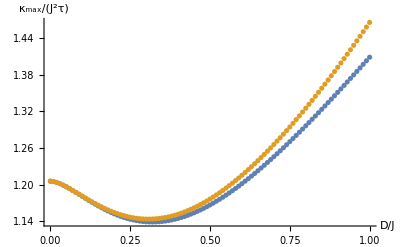

```mathematica
ListPlot[{Table[{sophblistconstT[[i]][[2]],sophblistconstT[[i]][[3]]},{i,1,Length[sophblistconstT]}],Table[{sortedlargetest[[i]][[2]],sortedlargetest[[i]][[3]]},{i,1,Length[sortedlargetest]}]},PlotRange->All,AxesLabel->{Style["D/J",18],Style["κ_max/(J^2τ)",18]}]
```

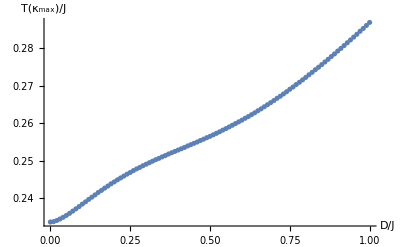

```mathematica
ListPlot[Table[{sortedlargetest[[i]][[2]],sortedlargetest[[i]][[1]]},{i,1Length[sortedlargetest]}],PlotRange->All,AxesLabel->{Style["D/J",18],Style["T(κ_max)/J",18]}]
```

```mathematica
listempiric=Table[{Log[T],Log[1/(4π^2)*NIntegrate[heatconductivitydensityempiric[kx,ky,1,1/T,ξcomb][kx,ky,1/T,1],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]]},{T,0.1,0.2,0.0001}];
```

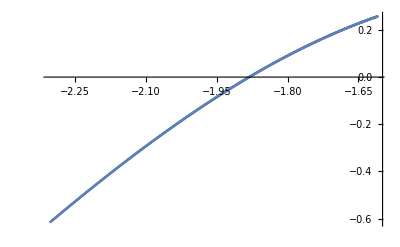

```mathematica
ListPlot[listempiric]
```

```mathematica
Fit[listempiric,{1,x},x]
```

2.32006+1.24786 x

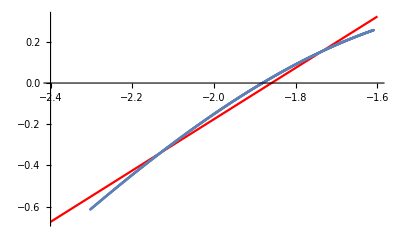

```mathematica
Show[Plot[2.3200559764379864+1.247855106615729 x,{x,-2.4,-1.6},PlotStyle->Red],ListPlot[listempiric]]
```

```mathematica
sorted=Sort[listempiric,#1[[2]]>#2[[2]]&];
counted=Count[Table[sorted[[i]][[2]],{i,1,Length[listempiric]}],listempiric[[1]][[2]]];
i=1;
While[i<=counted,
sorted=Delete[sorted,1];
i++;]
```

```mathematica
Fit[sorted,{1,x},x]
```

2.32093+1.24828 x

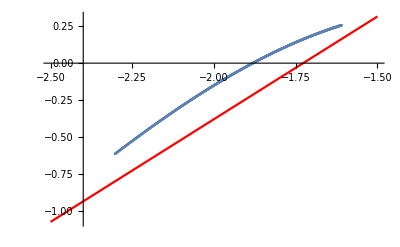

```mathematica
Show[Plot[2.4026857722722164+1.3910452661725858 x,{x,-2.5,-1.50},PlotStyle->Red],ListPlot[sorted]]
```

## Thermal Conductivity for narrowed Brillouin zone with empiric lifetime

center

```mathematica
Δ=π/10;
narrowedtocentersmallfield=ParallelTable[Table[{T,NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.01,1,0.01}],{d,0,0.01,0.001}];
narrowedtocenterlargefield=ParallelTable[Table[{T,NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-Δ,Δ},{ky,-Δ,Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.01,1,0.01}],{d,0.9,1,0.01}];
```

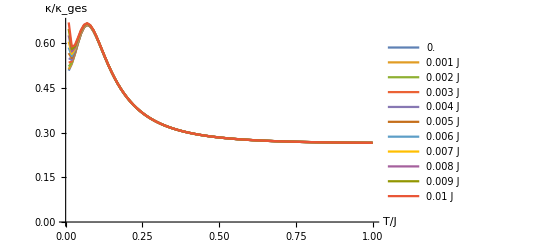

```mathematica
ListPlot[narrowedtocentersmallfield,PlotLegends->Table["J" N[0.01*i],{i,0,1,1/(Length[narrowedtocentersmallfield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]}]
```

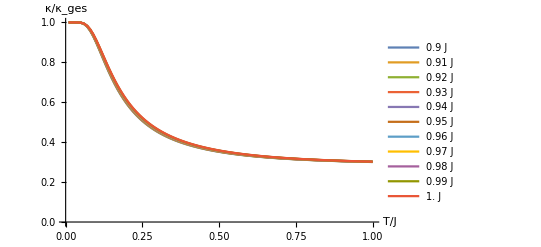

```mathematica
ListPlot[narrowedtocenterlargefield,PlotLegends->Table["J" N[i+0.9],{i,0,1,0.1/(Length[narrowedtocenterlargefield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```

edges

```mathematica
narrowedtoedgessmallfield=ParallelTable[Table[{T,4*NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,-π+Δ},{ky,-π,-π+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.01,1.0,0.01}],{d,0,0.1,0.01}];
narrowedtoedgeslargefield=ParallelTable[Table[{T,4*NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,-π+Δ},{ky,-π,-π+Δ},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]/NIntegrate[heatconductivitydensityempiric[kx,ky,d,1/T,ξcomb][kx,ky,1/T,d],{kx,-π,π},{ky,-π,π},MaxRecursion->100000,MinRecursion->90000,AccuracyGoal->100]},{T,0.01,1.0,0.01}],{d,0.9,1,0.01}];
```

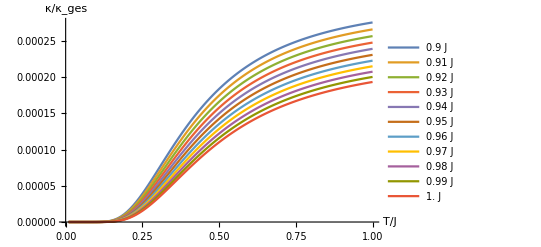

```mathematica
ListPlot[narrowedtoedgeslargefield,PlotLegends->Table["J" N[i+0.9],{i,0,1,0.1/(Length[narrowedtoedgeslargefield]-1)}],Joined->True,AxesLabel->{Style["T/J",18],Style["κ/κ_ges",18]},PlotRange->All]
```